## Gaussian moving potential

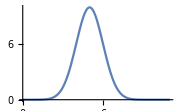

```mathematica
MovingGaus[a_, b_, c_, x_, ω_, t_]:= Chop[a*Chop[Exp[-(x- b*Sin[ω*t])^2/(2*c^2)]]];
Plot[MovingGaus[10, 5, 1, x, 1, Pi / 2], {x, 0, 11}, PlotRange->All, ImageSize-> Small]
```

```mathematica
TimeAverage[a_, b_, c_, x_]:= a/(2π)*Chop[Exp[(-2*x^2 - b^2)/(4*c^2)]]*Chop[NIntegrate[Chop[Exp[(x*b*Sin[t])/c^2]]*Chop[Exp[(b^2*Cos[2*t])/(4 c^2)]], {t, 0, 2π}]];
TimeAverageCentre[a_, b_, c_, x_]:= If[-1<x<1, a*Exp[-b^2/(4*c^2)]*BesselI[0, b^2/(4*c^2)], 0];
```

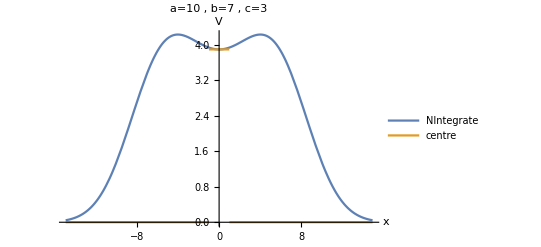

```mathematica
a = 10; b = 7; c = 3;Plot[{TimeAverage[a, b, c, x], TimeAverageCentre[a, b, c, x]} , {x, -15, 15}, PlotRange->All, PlotLegends->{"NIntegrate", "centre"}, AxesLabel->{x, V}, PlotLabel->("a="<>ToString[a]
", b="<>ToString[b]", c="<>ToString[c])]
```

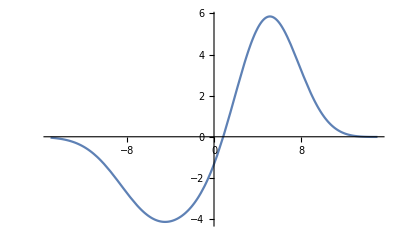

```mathematica
MovingGausMinusTimeAverage[a_, b_, c_, x_, ω_, t_]:= MovingGaus[a, b, c,x, ω, t] - TimeAverage[a, b, c, x];
Plot[MovingGausMinusTimeAverage[a, b, c, x, 3, 6*Pi/8], {x, -15, 15}, PlotRange->All]
```

```mathematica
TriRamp[high_, low_, radius_, i_]:= Table[(high-low)*UnitTriangle[x] + low, {x, -1, 1, 1/radius}][[i]];SL[ Nl_, centrex_, high_, low_, radius_]:=Table[If[MemberQ[Range[centrex-radius, +centrex+radius], i], TriRamp[high, low, radius, i-centrex+1+radius], -1], {i, 1, Nl}];
```

```mathematica
HtMovingGausMinusTimeAverage[Nl_,centrex_, a_, b_, c_,  ω_, t_]:=Table[If[i==j, MovingGausMinusTimeAverage[a, b, c, i -centrex,  ω, t],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
HtMovingGaus[Nl_,a_, b_, c_,  ω_, t_]:=Table[If[i==j, MovingGaus[a, b, c, i - Ceiling[Nl/2],  ω, t],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
HTimeIndependent[Nl_, centrex_,  high_, low_, radius_ ]:= Table[If[Abs[i-j]==1,SL[ Nl, centrex, high, low, radius][[Min[i, j]]],0], {i,1,Nl},{j,1,Nl}];
(*HTimeIndependent[ Nl_, hopsite_, newhoppingterm_]:= Table[If[Abs[i-j]==1,If[Ceiling[(i+j)/2]==hopsite, newhoppingterm, -1],0], {i,1,Nl},{j,1,Nl}];*)

HtMovingGausMinusTimeAverage[12,6, 10, 0.5, 0.3, 1, 0]//MatrixForm
HTimeIndependent[12, 6, -0.3, -1, 1] // MatrixForm
```

(0. | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0. | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0. | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | -5.15379×10^-6 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | -0.528501 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 4.38606 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | -0.528501 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | -5.15379×10^-6 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0. | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0. | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0. | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0.)

(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1. | 0 | -0.3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.3 | 0 | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

#### Solve Schrodinger Eq

```mathematica
ClearAll@ψ1;
ClearAll@ψ2;
Off[General::munfl]
(*conditions*)
tf = 30; Nl = 81; 
atomsitestart = 40;

(*time dependent potential parameters*)
a = 60; b = 0.05; c = 0.05; ω=3;
centrexM = 50;

(*stationary hopping parameters*)
centrexS = 50;
high = -0.07; low = -0.16; radius = 1;

ψ0 = Table[If[i==atomsitestart,1,0],{i,1,Nl}];
s1=NDSolve[{I D[ψ1[t], t]== HtMovingGausMinusTimeAverage[Nl, centrexM,a, b, c, ω, t].ψ1[t], ψ1[0] == ψ0}, ψ1, {t, 0, tf}];
ψ1[t_]=Evaluate[ψ1[t]/.s1]; 
s2=NDSolve[{I D[ψ2[t], t]== HTimeIndependent[Nl, centrexS, high, low, radius].ψ2[t], ψ2[0] == ψ0}, ψ2, {t, 0, tf}];
ψ2[t_]=Evaluate[ψ2[t]/.s2];
```

```mathematica
(*Table[Plot[Norm[ ψ[t][[1, i]]], {t, 0, 8*Pi / ω}, PlotRange->Full, PlotLabel -> i - midx, AxesLabel->{"t", ""}], {i, midx , midx+5}]*)
(*Table[Plot[Norm[ ψ[t][[1, i]]], {t, 0, tf}, PlotRange->{{0, 30}, {0, 1}}, PlotLabel -> i - midx, AxesLabel->{"t", ""}], {i, midx , midx+5}]*)
```

#### Plot things

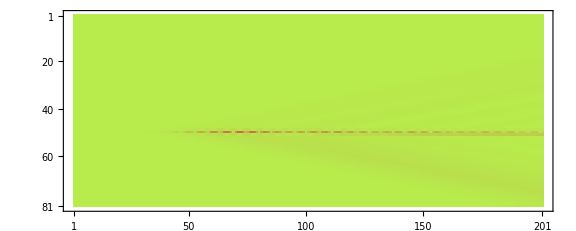

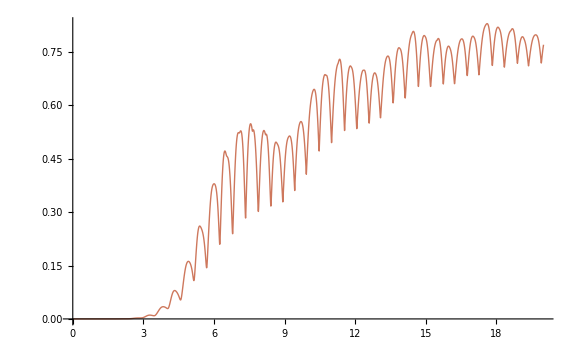

At tmax, sum is: 0.770273

-Graphics-

-Graphics-

Period: 2.0944

```mathematica
siteside = Floor[Nl/2];
siteside = 40; tmax = 20;

xrow=Table[If[Divisible[i, 10]==True,i/10,""],{i,0,tf*10}];
ycolumn=Table[ If[Divisible[i, 10]==True,i,""],{i,0,siteside*2}];
xticks=MapIndexed[{#2[[1]],#}&,xrow];
yticks=MapIndexed[{#2[[1]],#}&,ycolumn];

MatrixPlot[Table[Norm[ψ1[t][[1, i]] - ψ2[t][[1, i]]], {i, 1, Nl}, {t, 0, tmax, 0.1}],ColorFunction->"NeonColors", ColorFunctionScaling->False,  ImageSize->Large]
Plot[Total[Table[Norm[ψ1[t][[1, i]] - ψ2[t][[1, i]]], {i, 1, Nl}]], {t, 0, tmax}, PlotStyle->Thick, ColorFunction->Function[{x, y}, ColorData["NeonColors"][y]], ColorFunctionScaling->False]

Print["At tmax, sum is: ",Total[Table[Norm[ψ1[tmax][[1, i]] - ψ2[tmax][[1, i]]], {i, 1, Nl}]]]

 MatrixPlot[Table[Norm[ψ1[t][[1, i]]], {i, 1, Nl}, {t, 0, tmax, 0.1}], FrameLabel->{"site","t"}, FrameTicks->{{yticks,yticks},{xticks,xticks}}, ImageSize-> Full, ColorFunctionScaling->False, PlotLabel->"Time Dependent"]
MatrixPlot[Table[Norm[ψ2[t][[1, i]]], {i, 1, Nl}, {t, 0, tmax, 0.1}], FrameLabel->{"site","t"}, FrameTicks->{{yticks,yticks},{xticks,xticks}}, ImageSize-> Full, ColorFunctionScaling->False, PlotLabel->"Time Independent"]
Print["Period: ", N[2*Pi/ω]]
```